# POLINOMI

```mathematica
CurrentValue[EvaluationNotebook[], Background]=LightPurple
```

## SPLOŠNO O POLINOMIH:

Polinom imenovan tudi mnogočlenik ali veččlenik stopnje n, je linearna kombinacija potenc z nenegativnimi celimi eksponenti.

Polinome uvrščamo med cele racionalne funkcije. Preprosti polinomi so realne funkcije ene realne spremenljivke.

Splošni zapis polinoma je:

                                                                  p(x) = a_n x^n + a_(n-1)x^(n-1)+a_(n-2)x^(n-2)+ ... + a_2x^2+a_1x+a_0
     
 kjer so koeficienti a_n, a_(n-1),a_(n-2), .... , a_2,a_1,a_0 poljubna realna števila ali kompleksna števila, člen  a_n x^n je vodilni člen polinoma, koeficient a_0 je prosti koeficient ali tudi prosti člen, a_n pa je vodilni koeficient.
 
Vodilni člen polinoma vpliva na obliko grafa. Označimo jo z st(p).

Polinom ničte stopnje je konstantni polinom(primer f(x) = 2):

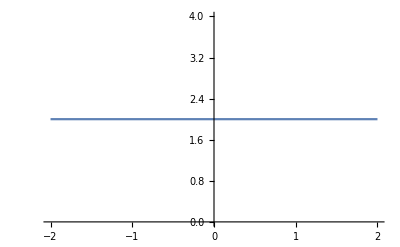

```mathematica
Plot[2,{x,-2,2}]
```

Polinom prve stopnje je linearna funkcija (primer f(x) = x + 3):

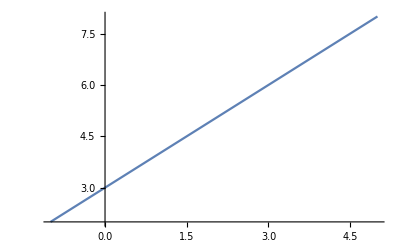

```mathematica
Plot[x+3,{x,-1,5}]
```

Polinom druge stopnje je kvadratna funkcija (primer f(x) = x^2 + 2x + 4):

```mathematica
Plot[x^2 +2x+4,{x,-12,10}]
```

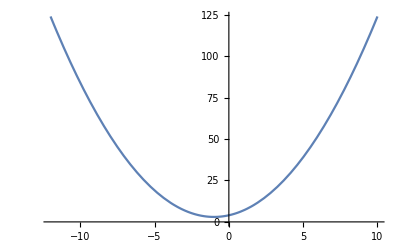

Polinom pete stopnje:  p(x) = x^5-4x^2+2x:

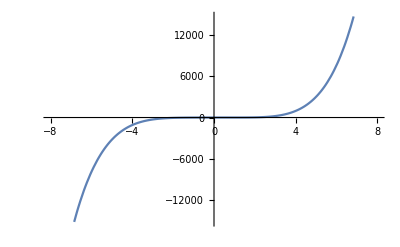

```mathematica
Plot[x^5-4 x^2+2x,{x,-8,8}]
```

Nad polinomi lahko izvajamo naslednje računske operacije:
	- množenje polinomov s konstanto
	- seštevanje polinomov
	- odštevanje polinomov
	- potenciranje polinomov
	- množenje polinomov
	- deljenje polinomov: v Mathematici poznamo funkcijo PolynomialQuotient, ki vrne količnik pri deljenju polinoma p(x) s polinomom q(x),  funkcija PolynomialRemainder pa vrne ostanek pri deljenju istih polinomov

```mathematica
p[x_]:=x^5−3x^3+2x^2+2x
```

```mathematica
q[x_]:=2x^3+2x−1
```

```mathematica
količnik =PolynomialQuotient[p[x],q[x],x]
```

-2+x^2/2

```mathematica
ostanek=PolynomialRemainder[p[x],q[x],x]
```

-2+6 x+(5 x^2)/2

## NIČLE POLINOMA:

Število x_0 je ničla polinoma če velja p (x_0) = 0. 

Polinom stopnje  n z realnimi koeficienti ima v množici realnih števil največ n ničel, v množici kompleksnih pa natanko n ničel. Tak polinom stopnje n lahko zapišemo v razcepljeni (ničelni) obliki:

	                                                                            p(x) = a *( x - x_1)*(x - x_2)*...*(x - x_n)

Pri iskanju ničel najpogosteje uporabljamo:
	- Razstavljanje: polinom razstavimo po pravilih za razstavljanje izrazov in iz razstavljenee oblike razberemo ničle

ZGLED ISKANJA NIČEL Z RAZSTAVLJANJEM
  V Mathemetici si lahko pomagamo s funkcijo Solve.  Poglejmo si na primeru:
	                   p(x) = x^5-7 x^4+19 x^3-25 x^2+1
Napišemo enačbo p(x) == 0, funkcija Solve pa vrne vse ničle polinoma.

```mathematica
Solve[x^5−7x^4+19x^3−25x^2+16x−4==0]
```

{{x→1},{x→1},{x→1},{x→2},{x→2}}

Lahko pa si pomagamo tudi s funkcijo Simplify, ki izraz oziroma v našem primeru 
polinom zapiše v najpreprostejši obliki.

```mathematica
Simplify[x^5−7x^4+19x^3−25x^2+16x−4]
```

(-2+x)^2 (-1+x)^3

- Hornerjev algoritem: Hornerjev algoritem je matematični algoritem, ki se uporablja pri računanju s polinomi. Postopek se imenuje po 		  angleškem matematiku Williamu Georgeu Hornerju. Bistvo algoritma se skriva v dejstvu, da se lahko polinom predstavi z njegovimi    koeficienti, ki se jih zapiše po vrsti(od najvišje potence do najnižje potence):

ZGLED ISKANJA NIČEL S HORNERJEVIM ALGORITMOM:
-Graphics-
S tem smo našli prvo ničlo polinoma p(x) in ga sedaj lahko zapišemo kot produkt:
p(x) = (x + 1) * (x^2 - 4x -5)
ta produkt pa lahko še naprej razstavimo na produkt:
p(x) = (x + 1) * (x - 5) * (x + 1)
p(x) = (x - 5) * (x + 1)^2

## GRAF POLINOMA:

Polinom je zvezna funkcija. To pomeni, da je graf polinoma nepretrgana krivulja. Pri risanju grafa polinoma upoštevamo naslednja pravila:

- Graf polinoma, ko gre x proti ±∞, je podoben grafu vodilnega člena tega polinoma ( y = a_n x^n). Torej je podoben grafu spotenčne funkcije	y = x^n raztegnjene z raztegom v smeri osi y za a_n.

- Graf polinoma v okolici ničle k-te stopnje je podoben grafu potenčne funkcije y = k^x.

- Pri risanju grafov moramo biti pozorni tudi na začetno vrednost polinoma.

NEKAJ PRIMEROV:
1. p(x) =  x^3in q(x) = 4 x^3-8 x^2-11x-3: vzamemo p(x) in q(x), ki imata enako stopnjo in iz tega vidimo, da se polinom obnaša podobno kot funkcija x^3

```mathematica
q[x_]:=4x^3-8x^2-11x-3
p[x_] := x^3
```

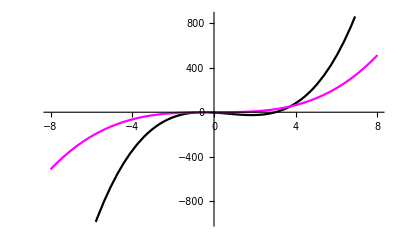

```mathematica
Plot[{q[x],p[x]},{x,-8,8},PlotStyle->{Black,Magenta}]
```

2. f(x) = 2 x^a + 4 x^(a-1)+ 6

```mathematica
f[x_,a_]:= 2 x^a + 4 x^(a-1)+ 6
Manipulate[Plot[f[x,a],{x,-10,10},PlotRange->Automatic],{a,1,9}]
```